```mathematica
Integrate[x^3*Exp[-((m*ω)/ℏ)*x^2],{x,-Infinity,Infinity}]
```

ConditionalExpression[0,Re[(m ω)/ℏ]≥0]

```mathematica
ψ:=(2/a)*(Sin[(n*Pi*x)/a])^2
```

```mathematica
n:=1
```

```mathematica
Integrate[ψ,{x,(3*a)/8,(5*a)/8}]
```

1/4+1/(√2 π)

```mathematica
ψ
```

(2 Sin[(2 π x)/a]^2)/a

```mathematica
n:=2
```

```mathematica
Integrate[ψ,{x,(3*a)/8,(5*a)/8}]
```

(-2+π)/(4 π)

```mathematica
n:=3
```

```mathematica
Integrate[ψ,{x,(3*a)/8,(5*a)/8}]
```

1/12 (3+(2 √2)/π)

```mathematica
n:=4
```

```mathematica
Integrate[ψ,{x,(3*a)/8,(5*a)/8}]
```

1/4

```mathematica
n:=5
```

```mathematica
Integrate[ψ,{x,(3*a)/8,(5*a)/8}]
```

1/4-1/(5 √2 π)

```mathematica
En:=(1-n^2)*((Pi^2*ℏ^2)/(2*m*a^2))
```

```mathematica
En
```

-(12 π^2 ℏ^2)/(a^2 m)

```mathematica
Clear[n]
```

```mathematica
En
```

((1-n^2) π^2 ℏ^2)/(2 a^2 m)

```mathematica
ψ
```

(2 Sin[(n π x)/a]^2)/a

```mathematica
ψn:=Sqrt[2/a]*Sin[(n*Pi*x)/a]
```

```mathematica
ψ1:=Sqrt[2/a]*Sin[(Pi*x)/a]
```

```mathematica
n:=2
```

```mathematica
Integrate[ψn*ψ1*Subscript[V,0],{x,(3*a)/8,(5*a)/8}]/En
```

0

```mathematica
ψn
```

√2 √(1/a) Sin[(2 π x)/a]

```mathematica
n:=3
```

```mathematica
Integrate[ψn*ψ1*Subscript[V,0],{x,(3*a)/8,(5*a)/8}]/En
```

((1+√2) a^2 m V_0)/(8 π^3 ℏ^2)

```mathematica
n:=4
```

```mathematica
Integrate[ψn*ψ1*Subscript[V,0],{x,(3*a)/8,(5*a)/8}]/En
```

0

```mathematica
n:=5
```

```mathematica
Integrate[ψn*ψ1*Subscript[V,0],{x,(3*a)/8,(5*a)/8}]/En
```

-((3+√2) a^2 m V_0)/(72 π^3 ℏ^2)

```mathematica
n:=6
```

```mathematica
Integrate[ψn*ψ1*Subscript[V,0],{x,(3*a)/8,(5*a)/8}]/En
```

0

```mathematica
n:=7
```

```mathematica
Integrate[ψn*ψ1*Subscript[V,0],{x,(3*a)/8,(5*a)/8}]/En
```

(a^2 m V_0)/(72 √2 π^3 ℏ^2)

```mathematica
n:=8
```

```mathematica
Integrate[ψn*ψ1*Subscript[V,0],{x,(3*a)/8,(5*a)/8}]/En
```

0

```mathematica
n:=9
```

```mathematica
Integrate[ψn*ψ1*Subscript[V,0],{x,(3*a)/8,(5*a)/8}]/En
```

(a^2 m V_0)/(200 √2 π^3 ℏ^2)

```mathematica
n:=10
```

```mathematica
Integrate[ψn*ψ1*Subscript[V,0],{x,(3*a)/8,(5*a)/8}]/En
```

0

```mathematica
n:=11
```

```mathematica
Integrate[ψn*ψ1*Subscript[V,0],{x,(3*a)/8,(5*a)/8}]/En
```

-((5+3 √2) a^2 m V_0)/(1800 π^3 ℏ^2)

```mathematica
Psi:=Sqrt[2/a]*Sin[(Pi*x)/a]+Out[29]*Sqrt[2/a]*Sin[(3*Pi*x)/a]+Out[33]*Sqrt[2/a]*Sin[(5*Pi*x)/a]+Out[38]*Sqrt[2/a]*Sin[(7*Pi*x)/a]+Out[42]*Sqrt[2/a]*Sin[(9*Pi*x)/a]+Out[46]*Sqrt[2/a]*Sin[(11*Pi*x)/a]
```

```mathematica
Psi
```

√2 √(1/a) Sin[(π x)/a]+((1+√2) m Sin[(3 π x)/a] V_0)/(4 √2 (1/a)^(3/2) π^3 ℏ^2)-((3+√2) m Sin[(5 π x)/a] V_0)/(36 √2 (1/a)^(3/2) π^3 ℏ^2)+(m Sin[(7 π x)/a] V_0)/(72 (1/a)^(3/2) π^3 ℏ^2)+(m Sin[(9 π x)/a] V_0)/(200 (1/a)^(3/2) π^3 ℏ^2)-((5+3 √2) m Sin[(11 π x)/a] V_0)/(900 √2 (1/a)^(3/2) π^3 ℏ^2)

```mathematica
Subscript[V,0]:=(3*Pi^2*ℏ^2)/(m*a^2)
```

```mathematica
Psi
```

√2 √(1/a) Sin[(π x)/a]+(3 (1+√2) √(1/a) Sin[(3 π x)/a])/(4 √2 π)-((3+√2) √(1/a) Sin[(5 π x)/a])/(12 √2 π)+(√(1/a) Sin[(7 π x)/a])/(24 π)+(3 √(1/a) Sin[(9 π x)/a])/(200 π)-((5+3 √2) √(1/a) Sin[(11 π x)/a])/(300 √2 π)

```mathematica
a:=5
```

```mathematica
Psi
```

√(2/5) Sin[(π x)/5]+(3 (1+√2) Sin[(3 π x)/5])/(4 √10 π)-((3+√2) Sin[π x])/(12 √10 π)+Sin[(7 π x)/5]/(24 √5 π)+(3 Sin[(9 π x)/5])/(200 √5 π)-((5+3 √2) Sin[(11 π x)/5])/(300 √10 π)

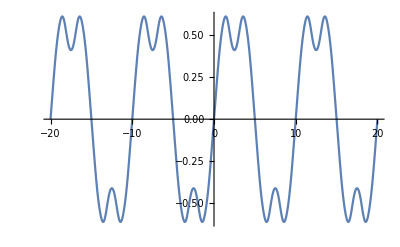

```mathematica
Plot[Psi,{x,-20,20}]
```

```mathematica
Clear[n,a]
```

```mathematica
ψ21:=(2/a)*Sin[(2*Pi*x)/a]*Sin[(Pi*y)/a]
```

```mathematica
ψ22:=(2/a)*Sin[(Pi*x)/a]*Sin[(2*Pi*y)/a]
```

```mathematica
ψ21
```

(2 Sin[(2 π x)/a] Sin[(π y)/a])/a

```mathematica
Subscript[V,0]
```

V_0

```mathematica
Clear[Subscript[V,0]]
```

Clear::ssym: V_0 is not a symbol or a string.

```mathematica
Subscript[V,0]:=(Pi^2*ℏ^2)/(4*m*a^2)
```

```mathematica
Subscript[V,0]
```

(π^2 ℏ^2)/(4 a^2 m)

```mathematica
H':=-Subscript[V,0]*Sin[(2*Pi*x)/a]*Sin[(2*Pi*y)/a]
```

```mathematica
H'
```

-(π^2 ℏ^2 Sin[(2 π x)/a] Sin[(2 π y)/a])/(4 a^2 m)

```mathematica
Integrate[ψ21*ψ21*H',{x,a/2,a},{y,0,a/2}]
```

ℏ^2/(3 a^2 m)

```mathematica
Integrate[ψ21*ψ22*H',{x,a/2,a},{y,0,a/2}]
```

-(64 ℏ^2)/(225 a^2 m)

```mathematica
Integrate[ψ22*ψ21*H',{x,a/2,a},{y,0,a/2}]
```

-(64 ℏ^2)/(225 a^2 m)

```mathematica
Integrate[ψ22*ψ22*H',{x,a/2,a},{y,0,a/2}]
```

ℏ^2/(3 a^2 m)

```mathematica
H:={{ℏ^2/(3 a^2 m),-(64 ℏ^2)/(225 a^2 m)},{-(64 ℏ^2)/(225 a^2 m),ℏ^2/(3 a^2 m)}}
```

```mathematica
H//MatrixForm
```

(ℏ^2/(3 a^2 m) | -(64 ℏ^2)/(225 a^2 m)
-(64 ℏ^2)/(225 a^2 m) | ℏ^2/(3 a^2 m))

```mathematica
Eigensystem[H]
```

{{(139 ℏ^2)/(225 a^2 m),(11 ℏ^2)/(225 a^2 m)},{{-1,1},{1,1}}}

```mathematica
a:=10
```

```mathematica
Plot3D[(2/a)*(-Sin[(2*Pi*x)/a]*Sin[(Pi*y)/a]+Sin[(Pi*x)/a]*Sin[(2*Pi*y)/a]),{x,0,a},{y,0,a}]
```

-Graphics3D-

```mathematica
Plot3D[(2/a)*(Sin[(2*Pi*x)/a]*Sin[(Pi*y)/a]+Sin[(Pi*x)/a]*Sin[(2*Pi*y)/a]),{x,0,a},{y,0,a}]
```

-Graphics3D-

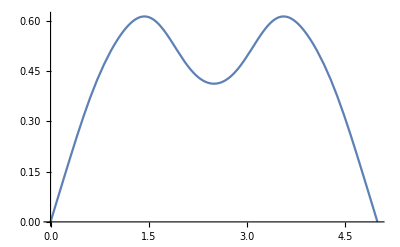

```mathematica
Plot[√(2/5) Sin[(π x)/5]+(3 (1+√2) Sin[(3 π x)/5])/(4 √10 π)-((3+√2) Sin[π x])/(12 √10 π)+Sin[(7 π x)/5]/(24 √5 π)+(3 Sin[(9 π x)/5])/(200 √5 π)-((5+3 √2) Sin[(11 π x)/5])/(300 √10 π),{x,0,5}]
```